```mathematica
(* DBI amplitude *)
Amp[s_,t_]:=Module[{u = -t-s},
-(Gamma[-t]Gamma[-u])/Gamma[1+s]-(Gamma[-s]Gamma[-u])/Gamma[1+t]-(Gamma[-s]Gamma[-t])/Gamma[1+u]];

Ker[s_,t_]:=1/s^2*1/(s+t);

g2 = SeriesCoefficient[Residue[Ker[s,t]*Amp[s,t],{s,0}]+Residue[Ker[s,t]*Amp[s,t],{s,-t}],{t,0,0}]

g3 = SeriesCoefficient[Residue[Ker[s,t]*Amp[s,t],{s,0}]+Residue[Ker[s,t]*Amp[s,t],{s,-t}],{t,0,1}]//FullSimplify
```

π^4/24

-1/2 π^2 Zeta[3]

```mathematica
g3/g2//N
```

-1.46153

```mathematica
Amp4d[s_,t_,m_]:=(-(Gamma[-t]Gamma[-u])/Gamma[1+(s-4m^2)]-(Gamma[-(s-4m^2)]Gamma[-u])/Gamma[1+t]-(Gamma[-(s-4m^2)]Gamma[-t])/Gamma[1+u])+(-(Gamma[-(t-4m^2)]Gamma[-u])/Gamma[1+s]-(Gamma[-s]Gamma[-u])/Gamma[1+(t-4m^2)]-(Gamma[-s]Gamma[-(t-4m^2)])/Gamma[1+u])+(-(Gamma[-t]Gamma[-(u-4m^2)])/Gamma[1+s]-(Gamma[-s]Gamma[-(u-4m^2)])/Gamma[1+t]-(Gamma[-s]Gamma[-t])/Gamma[1+(u-4m^2)])/.{u -> 4m^2-s-t};

Ker4d[s_,t_,s1_,s2_,k_]:= 1/(s-s1)*1/((s-s1)*(s-s2))^(k/2);

s1 = 2m^2;
s2 = 2m^2-t;
```

```mathematica
g24d = SeriesCoefficient[Residue[Ker4d[s,t,s1,s2,2]*Amp4d[s,t,m],{s,s1}]+Residue[Ker4d[s,t,s1,s2,2]*Amp4d[s,t,m],{s,s2}],{t,0,0}];
```

```mathematica
g34d = SeriesCoefficient[Residue[Ker4d[s,t,s1,s2,2]*Amp4d[s,t,m],{s,s1}]+Residue[Ker4d[s,t,s1,s2,2]*Amp4d[s,t,m],{s,s2}],{t,0,1}];
```

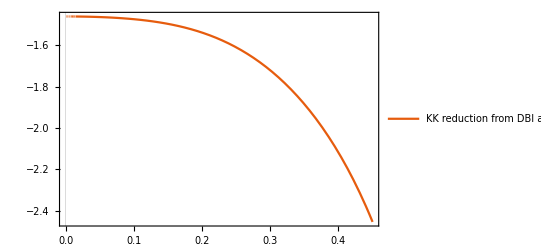

```mathematica
p4 = Plot[g34d/g24d,{m,1/10000`600,45/100`600},WorkingPrecision->600,PlotTheme->"Scientific",PlotRange->All, PlotLegends->{"KK reduction from DBI amp"}]
```

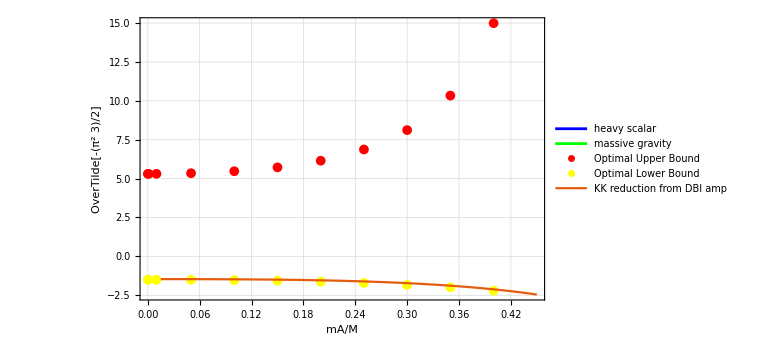

```mathematica
data1={{0`200,5.30624354498155`200},{0.001`200,5.30625916733434`200},{0.01`200,5.30781869969842`200},{0.05`200,5.34630310757489`200},{0.1`200,5.47538008276237`200},{0.15`200,5.72277490276586`200},{0.2`200,6.15033989170755`200},{0.25`200,6.87207325126097`200},{0.3`200,8.11853267109362`200},{0.35`200,10.337098209359`200},{0.4`200,14.9939610708506`200}};

data2 = {{0`200,-1.4999999999985`200},{0.001`200,-1.50000062016405`200},{0.01`200,-1.5003000600105`200},{0.05`200,-1.50753768844069`200},{0.1`200,-1.53061224489639`200},{0.15`200,-1.5706806282706`200},{0.2`200,-1.63043478260692`200},{0.25`200,-1.71428571428375`200},{0.3`200,-1.82926829268069`200},{0.35`200,-1.98675496688478`200},{0.4`200,-2.20588235293793`200}};

p1=ListPlot[data1,PlotStyle->{Red,PointSize[0.001]},PlotMarkers->{"●",10},PlotRange->All,PlotTheme->"Detailed",PlotLegends->{"Optimal Upper Bound"}];

p2=Plot[{r0[m,1`200],r[m,1`200]},{m,0`200,0.45`200},PlotStyle->{Blue,Green},PlotRange->All,WorkingPrecision->200,PlotTheme->"Detailed",PlotLegends->{"heavy scalar","massive gravity"}];

p3=ListPlot[data2,PlotStyle->{Yellow,PointSize[0.001]},PlotMarkers->{"●",10},PlotRange->All,PlotTheme->"Detailed",PlotLegends->{"Optimal Lower Bound"}];

plot=Show[p2,p1,p3,p4,Frame->True,FrameLabel->{Style[TraditionalForm[mA/M],16],Style[TraditionalForm[Overscript[g3,"~"]],16]},PlotRange->All,ImageSize->Large]
```

```mathematica
Export["C:\\Users\\User\\Pictures\\Screenshots\\plot.png",plot]
```

C:\Users\User\Pictures\Screenshots\plot.png

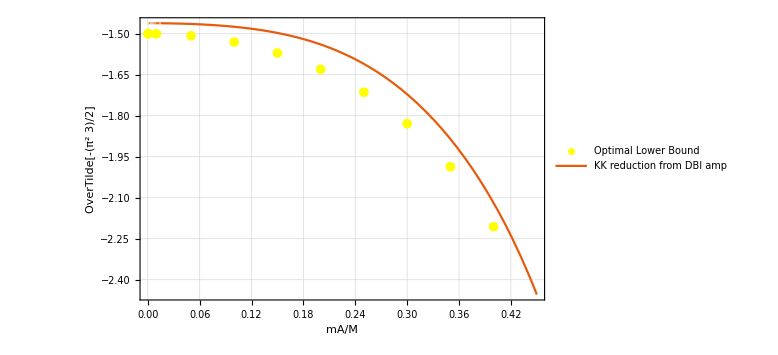

```mathematica
plot2=Show[p3,p4,Frame->True,FrameLabel->{Style[TraditionalForm[mA/M],16],Style[TraditionalForm[Overscript[g3,"~"]],16]},PlotRange->All,ImageSize->Large]
```

```mathematica
Export["C:\\Users\\User\\Pictures\\Screenshots\\plot2.png",plot2]
```

C:\Users\User\Pictures\Screenshots\plot2.png

```mathematica
s1p = 4m^2/3;
s2p = 8m^2/3-t;

g44d1 = SeriesCoefficient[Residue[Ker4d[s,t,s1p,s2p,2]*Amp4d[s,t,m],{s,s1p}]+Residue[Ker4d[s,t,s1p,s2p,2]*Amp4d[s,t,m],{s,s2p}],{t,4m^2/3,2}];

g44d2 = SeriesCoefficient[Residue[Ker4d[s,t,s1p,s2p,4]*Amp4d[s,t,m],{s,s1p}]+Residue[Ker4d[s,t,s1p,s2p,4]*Amp4d[s,t,m],{s,s2p}],{t,4m^2/3,0}];
n4 = g44d1-2*g44d2;
Print["n4 null constraint = ", n4//Simplify]
```

n4 null constraint = 0

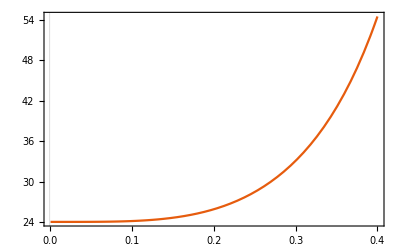

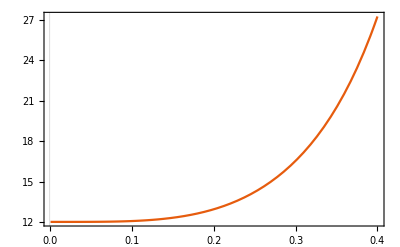

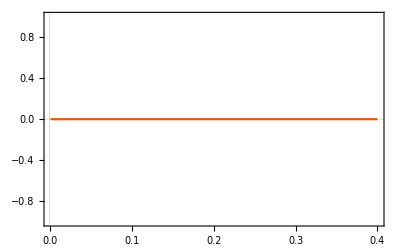

```mathematica
Plot[g44d1,{m,1/1000,4/10},WorkingPrecision->100,PlotRange->All,PlotTheme->"Scientific"]
Plot[g44d2,{m,1/1000,4/10},WorkingPrecision->100,PlotRange->All,PlotTheme->"Scientific"]
Plot[g44d1-2*g44d2,{m,1/1000,4/10},WorkingPrecision->100,PlotRange->All,PlotTheme->"Scientific"]
```